{0.0496037,Null}

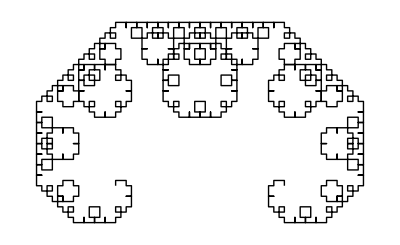

```mathematica
(*本蒟蒻写的渣代码*)
c={{-1,0},{1,0}};
f[x_,y_,z_,o_]={1/2 (-o+x+y+z),1/2 (o-x+y+z)};
Do[b=(f@@Flatten@Partition[c,2,1][[#]])&/@Range[Length[c]-1];c=Riffle[c,b],10];//AbsoluteTiming
Graphics@Line@c
```

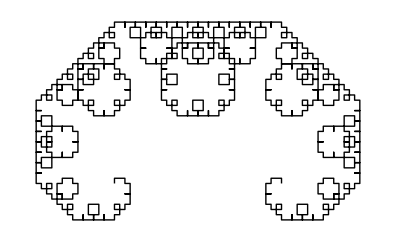
{0.00432014,-Graphics-}

```mathematica
(*这段代码由yxlllc巨佬改进，效率大增*)
f[x_,y_,z_,o_]={1/2 (-o+x+y+z),1/2 (o-x+y+z)};

Graphics@Line@Nest[Riffle[#,f@@@Flatten/@Partition[#,2,1][[;;Length[#]-1]]]&,{{-1,0},{1,0}},10]//AbsoluteTiming
```